```mathematica
bufferSingle={{123,110,108,107,112,107,105,106,106,107,106,107,106,128,106,106,106,107,105,106},{276,296,275,275,294,275,276,276,283,276,276,281,275,276,275,298,276,276,275,284},{522,536,522,538,522,538,522,545,522,545,522,522,542,522,538,522,546,522,538,522},{835,822,833,809,800,817,810,846,802,829,817,815,812,835,808,824,819,822,815,818}};
bufferSingleLocal={{31,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14},{15,15,15,15,14,15,15,15,14,15,15,15,15,15,15,15,15,14,15,14},{16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16},{45,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23}};
cubesSingle={{31,14,13,13,14,13,13,13,13,13,13,13,13,13,14,13,13,13,13,13},{33,33,32,32,33,32,33,33,32,32,32,33,33,33,32,32,33,47,33,33},{62,62,62,62,62,62,62,62,62,62,62,62,62,62,75,62,62,62,62,62},{102,102,102,102,102,102,125,102,102,102,102,102,102,102,102,102,123,102,102,102}};
cubesSingleLocal={{14,15,14,14,15,14,14,14,14,15,14,15,14,14,14,14,14,14,14,14},{16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,25,15,15},{15,15,15,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15},{21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21}};
```

```mathematica
single={{40,20,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18},{41,41,41,41,41,56,41,41,41,41,41,41,41,41,41,41,41,41,41,41},{80,80,80,80,101,80,80,80,80,80,80,80,80,80,80,80,89,80,80,80},{114,113,113,113,113,113,130,113,113,113,113,113,113,113,129,114,113,113,113,113}};
singleLocal={{14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14},{15,15,15,15,15,15,15,37,14,14,15,14,15,14,14,14,14,15,14,14},{15,15,16,16,16,15,15,16,15,15,16,15,15,15,16,15,16,15,15,15},{23,23,23,23,23,22,23,22,23,23,23,23,23,23,22,23,23,23,38,30}};
single16x16={{39,18,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16},{38,51,38,38,38,38,38,38,38,37,38,38,38,37,38,38,38,38,38,38},{68,68,68,68,88,69,69,68,69,69,69,69,69,69,69,69,69,69,81,69},{115,115,115,114,114,115,114,129,114,114,114,114,115,115,114,114,124,114,115,115}};
bufferSingle16x16={{41,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18},{45,57,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45},{85,108,85,85,85,85,85,85,85,85,85,85,85,100,85,85,85,85,85,85},{140,139,139,140,139,139,139,139,139,138,159,139,139,139,139,139,139,158,139,139}};
```

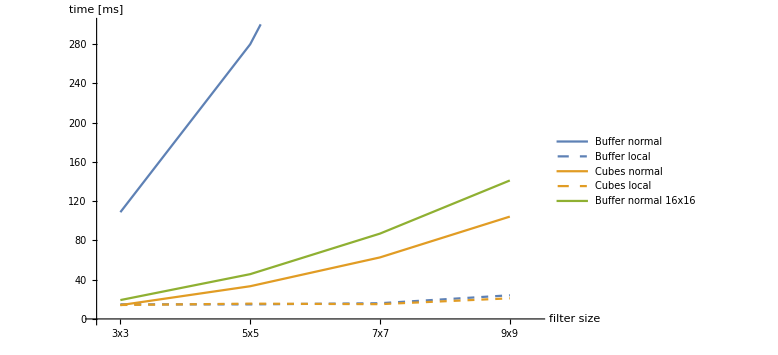

```mathematica
ListLinePlot[{Mean[bufferSingleᵀ],Mean[bufferSingleLocalᵀ],Mean[cubesSingleᵀ],Mean[cubesSingleLocalᵀ],Mean[bufferSingle16x16ᵀ]},
Ticks->{{{1,"3x3"},{2,"5x5"},{3,"7x7"},{4,"9x9"}}, Automatic},
PlotStyle->{Directive[RGBColor[0.368417, 0.506779, 0.709798],Line],Directive[RGBColor[0.368417, 0.506779, 0.709798],Dashed],Directive[RGBColor[0.880722, 0.611041, 0.142051],Line],Directive[RGBColor[0.880722, 0.611041, 0.142051],Dashed],Directive[RGBColor[0.560181, 0.691569, 0.194885],Line],Directive[RGBColor[0.560181, 0.691569, 0.194885],Dashed]},
PlotRange->{{0.8,4.2},{0,300}},
AxesLabel->{"filter size","time [ms]"},
PlotLegends->{"Buffer normal","Buffer local","Cubes normal","Cubes local","Buffer normal 16x16"},
ImageSize->Large,
BaseStyle->{FontSize->14}
]
```

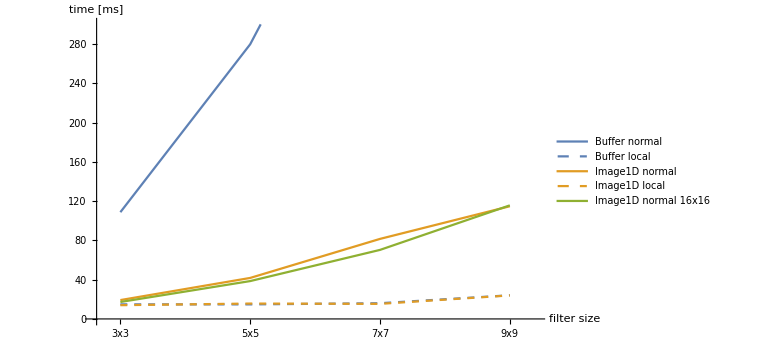

```mathematica
ListLinePlot[{Mean[bufferSingleᵀ],Mean[bufferSingleLocalᵀ],Mean[singleᵀ],Mean[singleLocalᵀ],Mean[single16x16ᵀ]},
Ticks->{{{1,"3x3"},{2,"5x5"},{3,"7x7"},{4,"9x9"}}, Automatic},
PlotStyle->{Directive[RGBColor[0.368417, 0.506779, 0.709798],Line],Directive[RGBColor[0.368417, 0.506779, 0.709798],Dashed],Directive[RGBColor[0.880722, 0.611041, 0.142051],Line],Directive[RGBColor[0.880722, 0.611041, 0.142051],Dashed],Directive[RGBColor[0.560181, 0.691569, 0.194885],Line],Directive[RGBColor[0.560181, 0.691569, 0.194885],Dashed]},
PlotRange->{{0.8,4.2},{0,300}},
AxesLabel->{"filter size","time [ms]"},
PlotLegends->{"Buffer normal","Buffer local","Image1D normal","Image1D local","Image1D normal 16x16"},
ImageSize->Large,
BaseStyle->{FontSize->14}
]
```